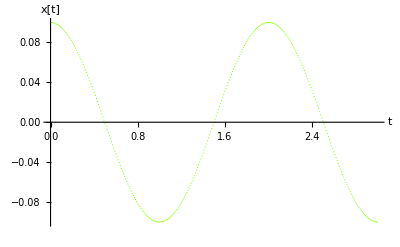

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

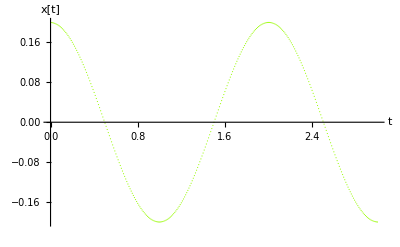

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

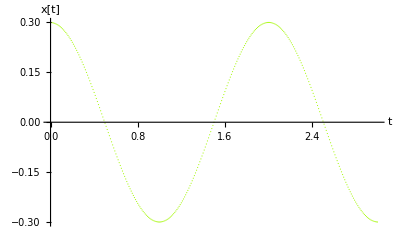

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

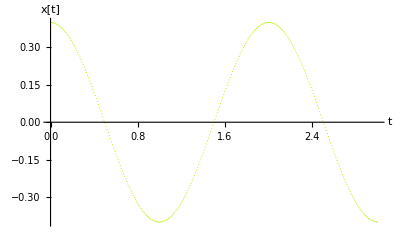

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

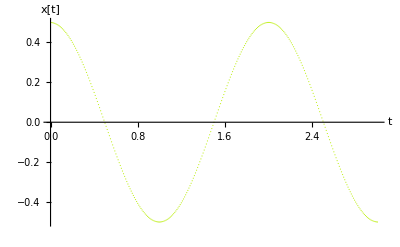

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

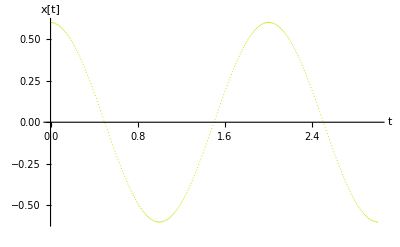

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

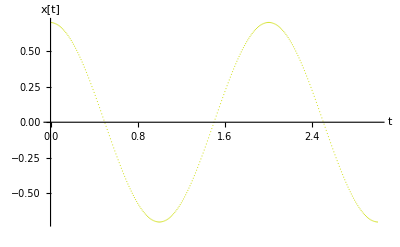

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

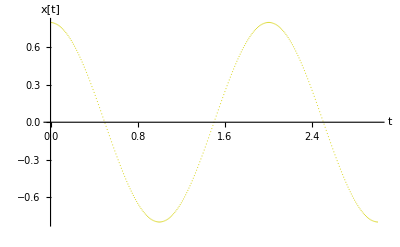

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

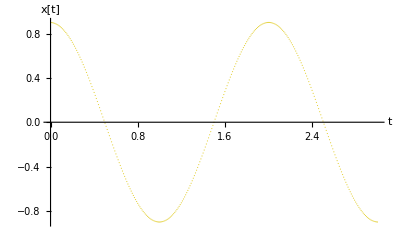

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

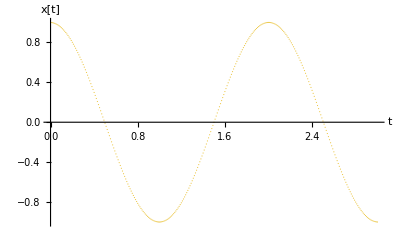

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

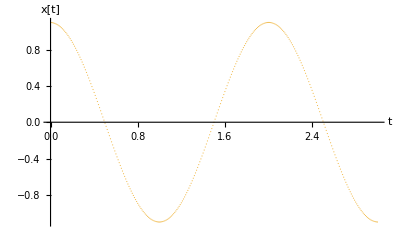

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

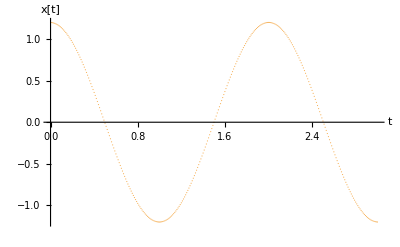

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

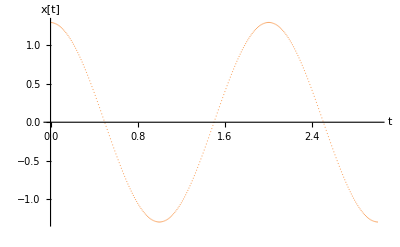

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

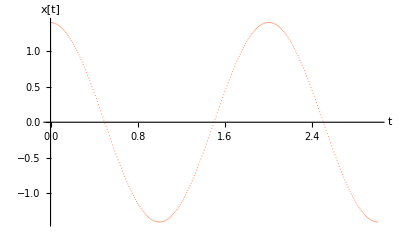

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

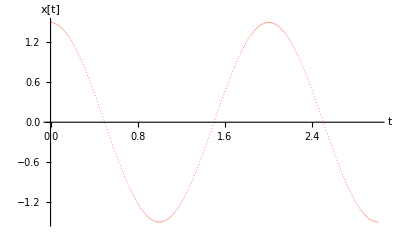

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

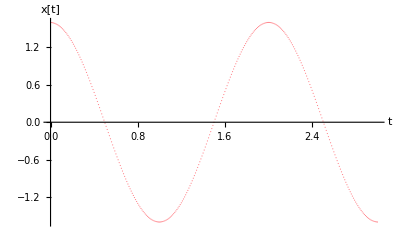

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

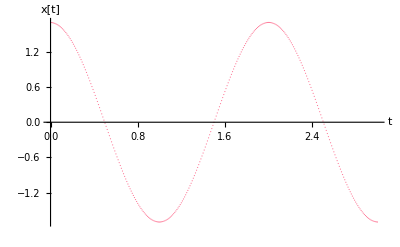

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

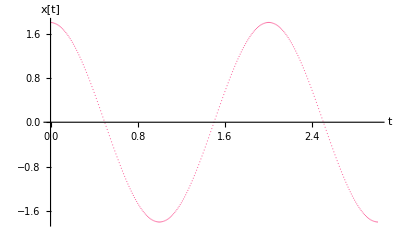

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

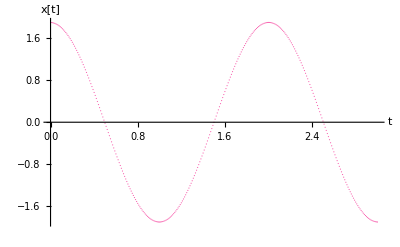

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

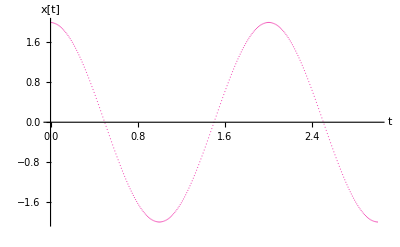

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

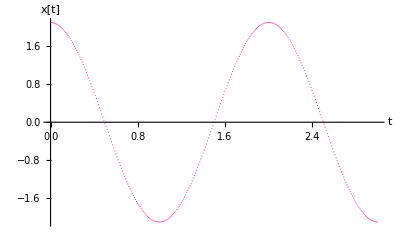

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

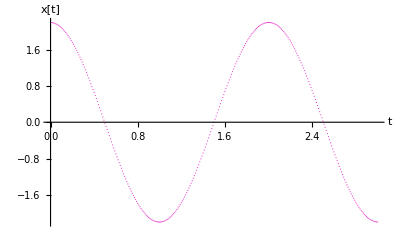

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

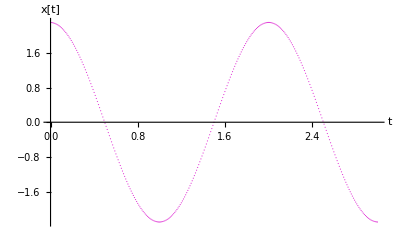

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

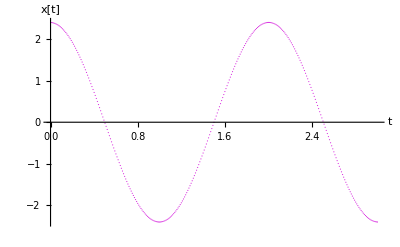

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

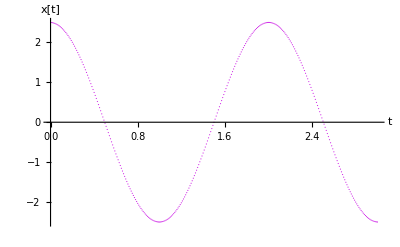

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

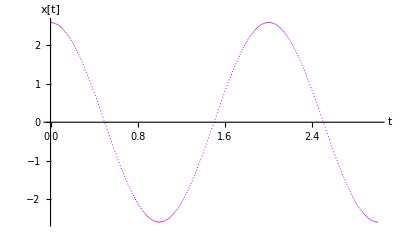

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

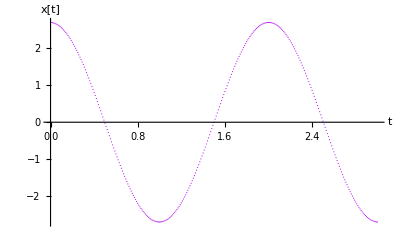

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

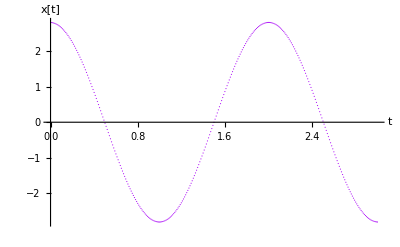

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

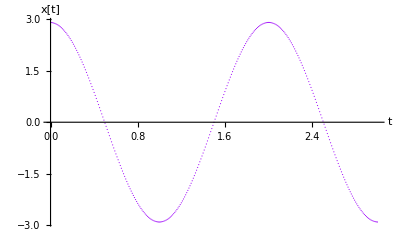

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

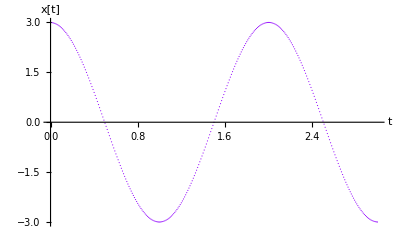

The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds

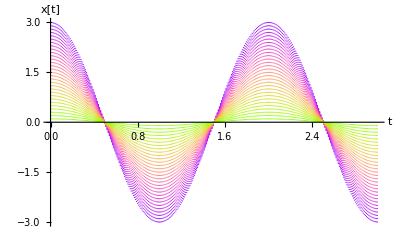

We see no change in the Period

```mathematica
(*Assignment of Variables*)
Clear[x,v,F,e];
m = 2;
k = 19.6;
Steps = 300;
Δt = .01;
x[0]=.1;
v[0]=0;
e[0]=0;
z=0;
plots={};

(*Question 1*)
For[
(*The size of the For Loop*)
x[0]=.0,
x[0]<3,
x[0]+=.1;

(*Calculates the Points, x[0] increments the starting postion*)

Do[
F[n]=-k*x[n];
v[n+1]=v[n]+(F[n]/m)*Δt;
x[n+1]=x[n]+v[n+1]*Δt;
e[n+1]=1/2*m*v[n+1]^2+1/2*k*x[n+1]^2,{n,0,Steps}
];
xdata = Table[{n*Δt,x[n]},{n,0,Steps}];



(*This Handles the Colored Graphs*)
z+=.1;
r=((Sin[z]+1)/2);
g=((Cos[z]+1)/2);
b=((-Cos[z]+1)/2);




(*Graphs the Points and Saves them to a List*)
xplot = ListPlot[
xdata,
AxesLabel->{"t","x[t]"},
PlotStyle->{
PointSize[0.002],
RGBColor[r,g,b]
}];
AppendTo[plots,xplot];
Print[xplot];
Print["The Period of this plot is T=2pi*sqrt[m/k] which is 2 seconds"];

];
(*Shows all Plots Saved*)
Show[Reverse[plots]]
Print["We see no change in the Period"]
```